# Code for the Article: Asghar Ullah, M.Tahir Naseem, and Ozgur E.Mustecaplıoglu, “Low-temperature quantum thermometry boosted by coherence generation, ”(2023), arXiv:2211.05461.

```mathematica
ClearAll["Global`*"]
```

### Code for Partial trace:

```mathematica
SwapParts[expr_,pos1_,pos2_]:=(ReplacePart[#1,#1,{pos1,pos2},{pos2,pos1}]&)[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];TrkM=D;z=Dimensions[Qubits][[1]]+1;
For[q=1,q<z,q++,n=Log[2,Dimensions[TrkM][[1]]];M=TrkM;k=Qubits[[q]];
If[k==n,TrkM={};For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<n-k,j++,b={0};For[i=1,i<2^n+1,i++,If[Mod[IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]],2]==1&&Count[b,i]==0,Permut={i,FromDigits[SwapParts[IntegerDigits[i-1,2,n],{n},{n-j-1}],2]+1};
b=Append[b,FromDigits[SwapParts[IntegerDigits[i-1,2,n],{n},{n-j-1}],2]+1];c=Range[2^n];
perm=SwapParts[c,{i},{FromDigits[SwapParts[IntegerDigits[i-1,2,n],{n},{n-j-1}],2]+1}];M=M[[perm,perm]];]];TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM])
```

### Pauli spin operators in computational basis and jump operators:

```mathematica
x ={{0,1},{1,0}}; 
Z={{1,0},{0,-1}};
y={{0,-Sqrt[-1]},{Sqrt[-1],0}};
id={{1,0},{0,1}};
sm = {{0,0},{1,0}};
sp = {{0,1},{0,0}};
sma = KroneckerProduct[sm, id];
spa = ConjugateTranspose[sma];
A2 = KroneckerProduct[sm, sp];
A2d= ConjugateTranspose[A2];
A3 =KroneckerProduct[sm, sm];
A3d = ConjugateTranspose[A3];
```

Original Hamiltonian of the system:
H=1/2 ω_p(σ^z)_p+1/2∑_k ω_k(σ^z)_k+∑_k g_k(σ^z)_k(σ^x)_p

```mathematica
Hd = ω1/2 KroneckerProduct[Z,id]+Ω/2KroneckerProduct[id,Z]; (*Diagonalized Hamiltonian of the probe-ancilla. ω1 is the frequency of ancilla qubit while Ω is defined below*)
```

```mathematica
ρ =Array[Subscript[ro,##][t]&,{4,4}]; (*General density matrix of order 4 by 4*)
```

```mathematica
(*Dissipators of the Master Equation*)
L1=Simplify[c2^2(sma.ρ.spa-(spa.sma.ρ+ρ.spa.sma)/2)+c2^2*Exp[-ω1/T](spa.ρ.sma-(sma.spa.ρ+ρ.sma.spa)/2)];
L2=Simplify[s2^2(A2.ρ.A2d-(A2d.A2.ρ+ρ.A2d.A2)/2)+ s2^2*Exp[-ωM/T](A2d.ρ.A2-(A2.A2d.ρ+ρ.A2.A2d)/2)];
L3=Simplify[s2^2(A3.ρ.A3d-(A3d.A3.ρ+ρ.A3d.A3)/2)+ s2^2*Exp[-ωP/T](A3d.ρ.A3-(A3.A3d.ρ+ρ.A3.A3d)/2)];
```

```mathematica
Dissip =L1+L2+L3; 
ℏ = 1;
dρ = -ⅈ*(Hd.ρ-ρ.Hd)/ℏ+Dissip; (*Full Master Equation*)
(* Steady state solution of the master equation in dressed basis *)
RH =dρ /. t->∞;
eqs∞ = Flatten[Table[Table[RH[[jj,kk]]==0,{jj,1,4}],{kk,1,4}]];
eqs∞ = Flatten[{eqs∞,Subscript[ro, 1,1][∞]+Subscript[ro, 2,2][∞]+Subscript[ro, 3,3][∞]+Subscript[ro, 4,4][∞]==1}];
sol∞ = Solve[eqs∞,{Subscript[ro, 1,1][∞],Subscript[ro, 1,2][∞],Subscript[ro, 1,3][∞],Subscript[ro, 1,4][∞],Subscript[ro, 2,1][∞],Subscript[ro, 2,2][∞],Subscript[ro, 2,3][∞],Subscript[ro, 2,4][∞],Subscript[ro, 3,1][∞],Subscript[ro, 3,2][∞],Subscript[ro, 3,3][∞],Subscript[ro, 3,4][∞],Subscript[ro, 4,1][∞],Subscript[ro, 4,2][∞],Subscript[ro, 4,3][∞],Subscript[ro, 4,4][∞]}];
solbak = Assuming[{ωa,Ω,T,c,s}∈Reals,FullSimplify[sol∞]];
ρ∞ = FullSimplify[ ρ /.t->∞/. solbak[[1]]/.{ωP->ω1+Ω,ωM->ω1-Ω}];
(* ρ∞ is the steady state solution of Master Equation*)
```

```mathematica
ρC=ρ∞;(*The combined state of probe and ancilla which is a Gibbs thermal state (In global basis)*)
```

```mathematica
ρC//MatrixForm
```

(1/((1+ⅇ^(Ω/T)) (1+ⅇ^(ω1/T))) | 0 | 0 | 0
0 | ⅇ^(Ω/T)/((1+ⅇ^(Ω/T)) (1+ⅇ^(ω1/T))) | 0 | 0
0 | 0 | ⅇ^(ω1/T)/((1+ⅇ^(Ω/T)) (1+ⅇ^(ω1/T))) | 0
0 | 0 | 0 | ⅇ^((Ω+ω1)/T)/((1+ⅇ^(Ω/T)) (1+ⅇ^(ω1/T))))

```mathematica
ρp=FullSimplify[TraceSystem[ρ∞,{1}]];(*reduced State for the probe qubit*)
```

```mathematica
ρA=FullSimplify[TraceSystem[ρ∞,{2}]];(*Reduced State for an ancilla qubit*)
```

```mathematica
ρp = {{1/(1+ⅇ^(Ω/T)),0},{0,1-1/(1+ⅇ^(Ω/T))}};
ρA={{1/(1+ⅇ^(ω1/T)),0},{0,1-1/(1+ⅇ^(ω1/T))}};
ρg = KroneckerProduct[ρA,ρp ];
```

Note: The combined state of ancilla+probe (global) is the same as the product state of ancilla and probe we defined above.

```mathematica
ρC-ρg//FullSimplify                 (*steady-state obtained from ME is the same as product state of thermal density matrices of two qubits*)
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*Here, we apply back transformation to get the density matrix in local basis*)
U= MatrixExp[-ⅈ θ/2 KroneckerProduct[Z,y]];
ρback=Assuming[{ω1,ωp,Ω}∈Reals,FullSimplify[Assuming[{θ} ∈Reals, FullSimplify[U.ρg.ConjugateTranspose[U]]]]];
ρb=FullSimplify[TraceSystem[ρback,{1}]];
```

```mathematica
(*Quantum Fisher information for the probe qubit--It may take few moments to simplify*)
ϕ=(Tr[(D[ρb,T])^2]+1/Det[ρb](Tr[(ρb.D[ρb,T])^2]))//FullSimplify;
```

```mathematica
Ω=Sqrt[ωp^2+4*(g)^2];
θ=ArcTan[2*g/ωp];
```

## Plots for QFI and Coherence with different values of coupling strength g:

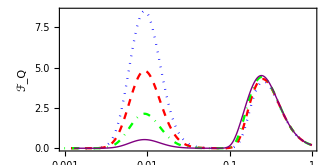

```mathematica
diff=Show[LogLinearPlot[ϕ/.{ω1->0.04,ωp->1, g->0.04}, {T,0,1},PlotRange->All,PlotStyle->{Thick,Blue,Dotted,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"","ℱ_Q"}],
LogLinearPlot[ϕ/.{ω1->0.04,ωp->1, g->0.03}, {T,0,1},PlotRange->All,PlotStyle->{Red,Dashed,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"","ℱ_Q"}],
LogLinearPlot[ϕ/.{ω1->0.04,ωp->1, g->0.02}, {T,0,1},PlotRange->All,PlotStyle->{Green,DotDashed,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"","ℱ_Q"}],
LogLinearPlot[ϕ/.{ω1->0.04,ωp->1, g->0.01}, {T,0,1},PlotRange->All,PlotStyle->{Purple,Thick},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"","ℱ_Q"}]
,FrameTicks->Automatic,FrameStyle->Directive[Black,12],ImageSize->330,AspectRatio->1/2]
```

```mathematica
cohr=1/2 Sin[θ] Tanh[Ω/(2 T)] Tanh[ω1/(2 T)]+1/2 Sin[θ] Tanh[Ω/(2 T)] Tanh[ω1/(2 T)];
```

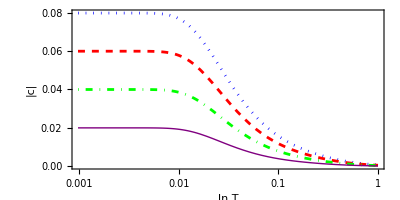

```mathematica
Show[LogLinearPlot[cohr/.{ω1->0.04,ωp->1, g->0.04}, {T,0,1},PlotRange->All,PlotStyle->{Blue,Dotted,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"ln T","|c|"}],
LogLinearPlot[cohr/.{ω1->0.04,ωp->1, g->0.03}, {T,0,1},PlotRange->All,PlotStyle->{Red,Dashed,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"ln T","|c|"}],
LogLinearPlot[cohr/.{ω1->0.04,ωp->1, g->0.02}, {T,0,1},PlotRange->All,PlotStyle->{Green,DotDashed,Thickness[0.005]},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"ln T","|c|"}],
LogLinearPlot[cohr/.{ω1->0.04,ωp->1, g->0.01}, {T,0,1},PlotRange->All,PlotStyle->{Purple,Thick},Frame->True,FrameStyle->Directive[Black,12],FrameLabel->{"ln T","|c|"}],FrameTicks->Automatic,FrameStyle->Directive[12,Black],AspectRatio->1/2]
```